```mathematica
WolframLanguadeData[]
```

WolframLanguadeData[]

```mathematica
WolframLanguageData[];
```

```mathematica
?WolframLanguageData
```

```mathematica
WolframLanguageData["Plot","DocumentationExampleInputs"][[1]]
```

BasicExamples→{{Plot[Sin[x],{x,0,6Pi}]},{Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotLegends→Expressions]},{Plot[{Sin[x],Cos[x]},{x,0,2Pi},PlotLabels→Expressions]},{Plot[2Sin[x]+x,{x,0,15},Filling→Bottom],Plot[{Sin[x]+x/2,Sin[x]+x}, {x, 0, 10},Filling→{1→{2}}]},{Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling→Axis]}}

```mathematica
WolframLanguageData["Write","PlaintextUsage"]//
```

Write[channel, expr1, expr2, …] writes the expressions expri in sequence, followed by a newline, to the specified output channel.

```mathematica
(* For which errors I'm I trying to provide info *)
```

```mathematica
correct="Plot[5x^2,{x,0,2}]";
```

```mathematica
wrong=correct="Plot[5x^2,{x,0,2]}";
```

```mathematica
SyntaxInformation[Plot]
```

{ArgumentsPattern→{_,_,OptionsPattern[]},LocalVariables→{Plot,{2}}}

```mathematica
SyntaxInformation[Write]
```

{ArgumentsPattern→{__}}

```mathematica
Write["stdout"]
```

```mathematica
?Write
```

```mathematica
SyntaxInformation[GaussianFilter]
```

{ArgumentsPattern→{_,_,Optional[{__}],OptionsPattern[]}}

```mathematica
(* Maybe, compare the heads, *)
```

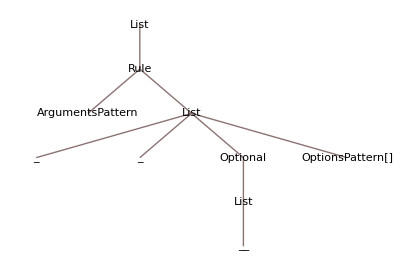

```mathematica
TreeForm[%2]
```

```mathematica
%2[[1,2]]
```

```mathematica
thislist= {1,1,2,1,4,3,4,3,2,4,2};
```

```mathematica
GaussianFilter[thislist,2]
```

{1.05088,1.21184,1.62721,1.94912,3.05088,3.32191,3.47456,3.05088,2.73728,3.,2.42368}

```mathematica
SyntaxInformation[GaussianFilter][[1,2]]
```

{_,_,Optional[{__}],OptionsPattern[]}

```mathematica
Hold[GaussianFilter[thislist,2]]
```

Hold[GaussianFilter[thislist,2]]

```mathematica
%11
```

Hold[GaussianFilter[thislist,2]]

```mathematica
thislist=.
```

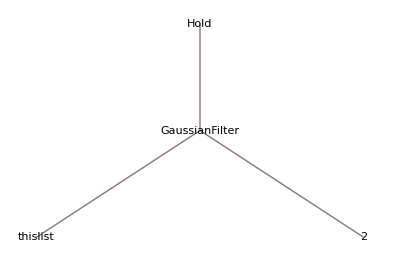

```mathematica
%11//TreeForm
```

```mathematica
Apply[Head,%91,1]// ReleaseHold
```

Head::argx: Head called with 2 arguments; 1 argument is expected.

Head[thislist,2]

```mathematica
Thread[f[%91],3]
```

f[Hold[GaussianFilter[thislist,2]]]

```mathematica
CMD + SHIFT + E
```

```mathematica
Apply@%11
```

Cell[BoxData[
 RowBox[{"Apply", "[", 
  RowBox[{"Hold", "[", 
   RowBox[{"GaussianFilter", "[", 
    RowBox[{"thislist", ",", "2"}], "]"}], "]"}]}]], "Output",
 CellChangeTimes->{{3.770720966573884*^9, 3.770720979950595*^9}},
 CellLabel->"Out[88]="]

```mathematica
%107//TreeForm
```

-Graphics-

direct call to the parser:

```mathematica
FrontEndExecute[FrontEnd`ReparseBoxStructurePacket["Exp[1+2"]]
```

RowBox[{Exp,[,RowBox[{1,+,2}]}]

```mathematica
FrontEndExecute[FrontEnd`ReparseBoxStructurePacket["Exp[1+2]"]]
```

RowBox[{Exp,[,RowBox[{1,+,2}],]}]

```mathematica
parseString[str_String]:=FrontEndExecute[FrontEnd`ReparseBoxStructurePacket[str]];
```

```mathematica
g[f[x]
```

```mathematica
FrontEndExecute[FrontEnd`ReparseBoxStructurePacket["g[f[x]"]]
```

RowBox[{g,[,RowBox[{f,[,x,]}]}]

```mathematica
Flatten@ReplaceRepeated[RowBox[{"g","[",RowBox[{"f","[","x","]"}]}], RowBox[{anything___}]:>{anything}]
```

{g,[,f,[,x,]}

```mathematica
Flatten@ReplaceRepeated[RowBox[{"g","[",RowBox[{"f","[","x","]"}]}], RowBox[{anything___}]:>{anything}]
```

```mathematica
flattenParse[exp_]:=Flatten@ReplaceRepeated[exp, RowBox[{anything___}]:>{anything}]
```

```mathematica
flattenParse@parseString["Exp[1+2*(Sin[x]]"]
```

{Exp,[,1,+,2,*,(,Sin,[,x,],]}

```mathematica
Names[""]
```

{}

If names return a non empty list, I can use that as the head of the symbol //Cases

then get the syntax

Maybe list all the possible combinations of brackets...

```mathematica
Names["Exp"]
```

{Exp}

```mathematica
SyntaxInformation[Exp]
```

{ArgumentsPattern→{_},LocalVariables→None,ColorEqualSigns→None}

```mathematica
Names["2"]
```

{}

```mathematica
...Exp[1+2+f[x,y],5]...
```

Try to construct all the possible trees: add bracket, remove bracket, moving bracket

```mathematica
SetAttributes[f,{HoldFirst}]
```

```mathematica
f[2+2,2+3]
```

f[2+2,5]

```mathematica
ToString[2+2,InputForm]
```

```mathematica
"4"
```

```mathematica
ToString[..., InputForm]
```

```mathematica
SetAttributes[makeExpressionString, {HoldFirst}]
makeExpressionString[exp_]:=StringTake[ToString[HoldComplete[exp], InputForm], {StringLength["HoldComplete["]+1,-StringLength["]"]-1}]
```

```mathematica
makeExpressionString[Exp[1+2 * 3]]
```

Exp[1 + 2*3]

```mathematica
makeExpressionString[Plot[{Sin[x]+x/2,Sin[x]+x}, {x, 0, 10},Filling->{1->{2}}]]
```

Plot[{Sin[x] + x/2, Sin[x] + x}, {x, 0, 10}, Filling -> {1 -> {2}}]

```mathematica
StringPosition["Plot[{Sin[x] + x/2, Sin[x] + x}, {x, 0, 10}, Filling -> {1 -> {2}}]","]"]
```

{{12,12},{26,26},{67,67}}

```mathematica
StringDrop["Plot[{Sin[x] + x/2, Sin[x] + x}, {x, 0, 10}, Filling -> {1 -> {2}}]", {26,26}]
```

Plot[{Sin[x] + x/2, Sin[x + x}, {x, 0, 10}, Filling -> {1 -> {2}}]

```mathematica
DeleteCases[flattenParse@parseString["Plot[{Sin[x] + x/2, Sin[x + x}, {x, 0, 10}, Filling -> {1 -> {2}}]"], " "]
```

```mathematica
{"Plot","[","{","Sin","[","x","]","+","x","/","2",",","Sin","[","x","+","x","}",",","{","x",",","0",",","10","}",",","Filling","->","{","1","->","{","2","}","}","]"}
```

```mathematica
"2 + 2"
```

```mathematica
stringExp=StringTake["HoldComplete[Exp[1 + 2 + Sin[x]]]" , {StringLength["HoldComplete["]+1,-StringLength["]"]-1}]
```

Exp[1 + 2 + Sin[x]]

```mathematica
flattenParse@parseString[stringExp]
```

{Exp,[,1, ,+, ,2, ,+, ,Sin,[,x,],]}

## From Giulio and Tim:

```mathematica
WolframLanguageData["Plot","DocumentationExampleInputs"];
```

```mathematica
SyntaxInformation[Cos]
```

{ArgumentsPattern→{_},LocalVariables→None,ColorEqualSigns→None}

```mathematica
parseString[str_String]:=FrontEndExecute[FrontEnd`ReparseBoxStructurePacket[str]];
```

```mathematica
flattenParse[exp_]:=Flatten@ReplaceRepeated[exp, RowBox[{anything___}]:>{anything}]
```

```mathematica
flattenParse@parseString["Exp[1+2*(Sin[x]]"]
```

{Exp,[,1,+,2,*,(,Sin,[,x,],]}

```mathematica
SetAttributes[makeExpressionString, {HoldFirst}]
makeExpressionString[exp_]:=StringTake[ToString[HoldComplete[exp], InputForm], {StringLength["HoldComplete["]+1,-StringLength["]"]-1}]
```

```mathematica
makeExpressionString[Plot[{Sin[x]+x/2,Sin[x]+x}, {x, 0, 10},Filling->{1->{2}}]]
```

Plot[{Sin[x] + x/2, Sin[x] + x}, {x, 0, 10}, Filling -> {1 -> {2}}]

```mathematica
StringPosition["Plot[{Sin[x] + x/2, Sin[x] + x}, {x, 0, 10}, Filling -> {1 -> {2}}]","]"]
```

```mathematica
StringDrop["Plot[{Sin[x] + x/2, Sin[x] + x}, {x, 0, 10}, Filling -> {1 -> {2}}]", {26,26}]
```

```mathematica
DeleteCases[flattenParse@parseString["Exp[1+2*(Sin[x]]"],"  "]
```

{Exp,[,1,+,2,*,(,Sin,[,x,],]}

### I will start with trigonometric functions that can only accept one argument

Choose an expression, then remove the final bracket for now:

```mathematica
myexpressionstring = "Exp[1+2*(Sin[x])]"
```

Exp[1+2*(Sin[x])]

```mathematica
bracketpositions=StringPosition[myexpressionstring,"]"]
```

{{15,15},{17,17}}

```mathematica
brackettodrop=bracketpositions[[-1]]
```

{17,17}

```mathematica
mybrokenexpressionstring= StringDrop[myexpressionstring,brackettodrop]
```

Exp[1+2*(Sin[x])

```mathematica
flattenParse@parseString[mybrokenexpressionstring]
```

{Exp,[,1,+,2,*,(,Sin,[,x,],)}

```mathematica
myexpression=DeleteCases[flattenParse@parseString[mybrokenexpressionstring],"  "]
```

{Exp,[,1,+,2,*,(,Sin,[,x,],)}

```mathematica
myexpression
```

{Exp,[,1,+,2,*,(,Sin,[,x,],)}

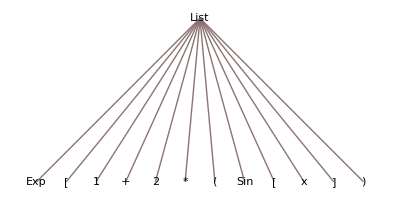

ⅇ^(1+2 Sin[x])

```mathematica
myexpression//TreeForm
```

Tim said, that every time a [ is found, go a level down. Try to do that.

Or maybe start with turning the function names from String to objects

```mathematica
ReplaceRepeated[myexpression, "[":>"["]
```

{Exp,[[,1,+,2,*,(,Sin,[[,x,],)}

```mathematica
StringCases["StyleBox[\"string\", \"TI\"]",lhs->rhs]
```